```mathematica
CurrentValue[EvaluationNotebook[],WindowElements]=Inherited
```

{StatusArea,MemoryMonitor,MagnificationPopUp,HorizontalScrollBar,VerticalScrollBar,MenuBar}

# Exploring Neural Networks

We have seen in class that a neural network is “just” an example of a multivariate function. The challenging part, if to actually find the right function that will assign the desired outputs to the given input data. The process of finding this function is called training the neural network. This is what people commonly refer to as learning.

Training a neural network is a complicated task that we will learn in the next few days. Thankfully, Mathematica has a set of pretrained NNs that are ready to be used on real data!

The neural network below was built to classify numbers from the MNIST dataset. The input of MNIST is a 28x28 grayscale image, and that the output is an integer number between 0 and 9. Mathematically, this will be a function from . You may wonder why , if we want the output to be a single digit. The reason is that ultimately the output will be a vector of length 10, in which each entry is the probability of that digit being 0, 1, 2, 3, 4, 5, 6, 7, 8 or 9. 

After loading the model, click on the + sign. You’ll see a list representing the composition of all functions that form the neural network. This one in particular is the composition of 11 different functions (or layers):

```mathematica
net=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

Once it is loaded, we can test it in some images. For the image below, it returns the correct value. Note that we called our network net, so in order to evaluate it we should refer to it by its name:

```mathematica
net[-Graphics-]
```

8

We can test it a few values at once. It seems to work well so far.

```mathematica
net[{-Graphics-, -Graphics-, -Graphics-}]
```

{6,8,0}

However, let’s try with numbers that don’t look that good! For example, the neural network thinks that the number below is an 8. Do you agree?

```mathematica
net[-Graphics-,"Probabilities"]
```

<|0→0.339992,1→0.00517717,2→0.000387435,3→0.00914817,4→0.0000222231,5→0.0598952,6→0.00883849,7→0.000383077,8→0.575069,9→0.00108666|>

What about the next one. Do you agree it is a 6?

```mathematica
net[-Graphics-]
```

6

We can also ask what the probability of it being each number is. For the one below, the network thinks it is either a 0 or a 6!

```mathematica
net[-Graphics-, "Probabilities"]
```

<|0→0.0558127,1→0.000220904,2→0.000190081,3→0.00219728,4→0.00316063,5→0.0383476,6→0.896179,7→2.01147×10^-6,8→0.0038771,9→0.0000130107|>

## Testing our own handwritten number!

Let’s try with our own image, and see how it performs. Say we draw an 8 by hand, and we want to ask the network what digit it is.

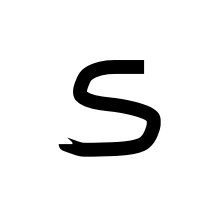
```mathematica
five=-Graphics-;
```

The network expects as input a 28x28 grayscale image, so we must change the color channels and the resolution accordingly.

```mathematica
five=ColorConvert[five,"Grayscale"];
five=ImageResize[five,{28,28}]
```

-Graphics-

The network does a good job!!!

```mathematica
net[five]
net[five,"Probabilities"]
```

5

<|0→4.8973×10^-6,1→4.39585×10^-7,2→0.000028887,3→0.000770553,4→2.14663×10^-7,5→0.993659,6→0.000120161,7→1.80229×10^-6,8→0.00284862,9→0.0025659|>

You try now!!! Use the sketchpad below to draw your own number. Afterwards, copy the image and paste it in the placeholder. Did it do a good job?

```mathematica
-Graphics-;
```

```mathematica
mynumber=ImageResize[ColorConvert[(*PASTE YOUR NUMBER HERE*),"Grayscale"],{28,28}]
```

-Graphics-

```mathematica
net[mynumber,"Probabilities"]
net[mynumber]
```

<|0→0.0000671014,1→0.00302123,2→0.00646462,3→0.942055,4→0.00302672,5→0.00450222,6→0.000204067,7→0.0039329,8→0.0230131,9→0.0137135|>

3

```mathematica
N[List@@net[-Graphics-,"Probabilities"],0]
```

{0.339992,0.00517717,0.000387434,0.00914816,0.0000222231,0.0598953,0.0088385,0.000383076,0.57507,0.00108666}

```mathematica
TeXForm[{0.3399,0.0052,0.0004,0.0091,0,0.0599,0.0088,0.0004,0.5751,0.0011}]
```

\{0.3399,0.0052,0.0004,0.0091,0,0.0599,0.0088,0.0004,0.5751,0.0011\}

## Other Pretrained Neural Networks:

The website https://resources.wolframcloud.com/NeuralNetRepository contains a collection of pre-trained neural networks for different purposes.

### Grayscale Image Colorization

Here is another example of a neural network that was trained to colorize grayscale images. In this case, the input and output are of the same size.

```mathematica
NetModel["Colorful Image Colorization Trained on ImageNet Competition Data"]
netevaluate[img_Image]:=
With[{lum=ColorSeparate[img,"L"]},
Image[Prepend[ArrayResample[NetModel["Colorful Image Colorization Trained on ImageNet Competition Data"][lum],
Prepend[Reverse@ImageDimensions@img,2]],ImageData[lum]],Interleaving->False,ColorSpace->"LAB"]]
```

NetChain[<>]

To test this Neural Network, we’ll load the infamous pepper image and transform it into grayscale.

```mathematica
peppers=ColorConvert[ExampleData[{"TestImage","Peppers"}],"Grayscale"]
```

-Graphics-

We can compare the computer-colorized image (left-hand side) to the original one (right hand side). Looks pretty good!!!

```mathematica
GraphicsRow[{netevaluate[pp],ExampleData[{"TestImage","Peppers"}]}]
```

-Graphics-

### Age Estimation

This neural network estimates the age of a person given a face-shot. This was me a year ago, apparently I was 27.

```mathematica
netage=NetModel["Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data"]
```

NetChain[<>]

```mathematica
netage[-Graphics-]
```

27

Let’s see how much I have aged:

```mathematica
netage[]
```

30

### Try Your Own Networks!